# Modelling and Control of One Leg Hopper

## Diagram

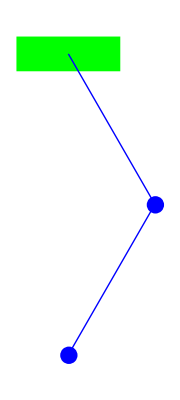

```mathematica
Graphics[{Thick,Green,Rectangle[{-0.3,-0.1},{0.3,0.1}],Thick,Blue,Line[{{0,0},{Sin[Pi/6],-Cos[Pi/6]}}], Thick, Blue,Disk[{Sin[Pi/6],-Cos[Pi/6]},0.05], Thick,Blue,Line[{{Sin[Pi/6],-Cos[Pi/6]},{Sin[Pi/6]+Sin[Pi/6-Pi/3],-Cos[Pi/6]-Cos[Pi/6-Pi/3]}}], Disk[{Sin[Pi/6]+Sin[Pi/6-Pi/3],-Cos[Pi/6]-Cos[Pi/6-Pi/3]},0.05]}]
```

# Writing Down the Lagrangian

```mathematica
ClearAll["Global`*"];
T[t_]=1/2 M0 (x'[t]^2+y'[t]^2) + 1/2 M1((l1 θ1'[t]Cos[θ1[t]]+x'[t])^2 + (l1 θ1'[t]Sin[θ1[t]]+y'[t])^2)+1/2 M2 ((l2 θ2'[t]Cos[θ1[t]+θ2[t]]+l1 θ1'[t]Cos[θ1[t]]+x'[t])^2+(l2 θ2'[t]Sin[θ1[t] + θ2[t]]+l1 θ1'[t]Sin[θ1[t]]+y'[t])^2);
V[t_]=M0 g y[t] + M1 g(y[t]-l1 Cos[θ1[t]]) + M2(y[t]-l1 Cos[θ1[t]]-l2 Cos[θ1[t]+θ2[t]]);
L[t_]=T[t]-V[t];
```

## Solving Dynamics Using Euler-Lagrange

Use the Euler-Lagrange equation to get the dynamics of each state variable.

```mathematica
dyn = Expand[{D[D[L[t],x'[t]],t] - D[L[t],x[t]], D[D[L[t],y'[t]],t] - D[L[t],y[t]], D[D[L[t],θ1'[t]],t] - D[L[t],θ1[t]], D[D[L[t],θ2'[t]],t] - D[L[t],θ2[t]]}]
```

{-l1 M1 Sin[θ1[t]] θ1'[t]^2-l1 M2 Sin[θ1[t]] θ1'[t]^2-l2 M2 Sin[θ1[t]+θ2[t]] θ1'[t] θ2'[t]-l2 M2 Sin[θ1[t]+θ2[t]] θ2'[t]^2+M0 x''[t]+M1 x''[t]+M2 x''[t]+l1 M1 Cos[θ1[t]] θ1''[t]+l1 M2 Cos[θ1[t]] θ1''[t]+l2 M2 Cos[θ1[t]+θ2[t]] θ2''[t],g M0+g M1+M2+l1 M1 Cos[θ1[t]] θ1'[t]^2+l1 M2 Cos[θ1[t]] θ1'[t]^2+l2 M2 Cos[θ1[t]+θ2[t]] θ1'[t] θ2'[t]+l2 M2 Cos[θ1[t]+θ2[t]] θ2'[t]^2+M0 y''[t]+M1 y''[t]+M2 y''[t]+l1 M1 Sin[θ1[t]] θ1''[t]+l1 M2 Sin[θ1[t]] θ1''[t]+l2 M2 Sin[θ1[t]+θ2[t]] θ2''[t],g l1 M1 Sin[θ1[t]]+l1 M2 Sin[θ1[t]]+l2 M2 Sin[θ1[t]+θ2[t]]+l2 M2 Sin[θ1[t]+θ2[t]] x'[t] θ2'[t]-l2 M2 Cos[θ1[t]+θ2[t]] y'[t] θ2'[t]+l1 l2 M2 Cos[θ1[t]+θ2[t]] Sin[θ1[t]] θ2'[t]^2-l1 l2 M2 Cos[θ1[t]] Sin[θ1[t]+θ2[t]] θ2'[t]^2+l1 M1 Cos[θ1[t]] x''[t]+l1 M2 Cos[θ1[t]] x''[t]+l1 M1 Sin[θ1[t]] y''[t]+l1 M2 Sin[θ1[t]] y''[t]+l1^2 M1 Cos[θ1[t]]^2 θ1''[t]+l1^2 M2 Cos[θ1[t]]^2 θ1''[t]+l1^2 M1 Sin[θ1[t]]^2 θ1''[t]+l1^2 M2 Sin[θ1[t]]^2 θ1''[t]+l1 l2 M2 Cos[θ1[t]] Cos[θ1[t]+θ2[t]] θ2''[t]+l1 l2 M2 Sin[θ1[t]] Sin[θ1[t]+θ2[t]] θ2''[t],l2 M2 Sin[θ1[t]+θ2[t]]-l2 M2 Sin[θ1[t]+θ2[t]] x'[t] θ1'[t]+l2 M2 Cos[θ1[t]+θ2[t]] y'[t] θ1'[t]+l2 M2 Cos[θ1[t]+θ2[t]] x''[t]+l2 M2 Sin[θ1[t]+θ2[t]] y''[t]+l1 l2 M2 Cos[θ1[t]] Cos[θ1[t]+θ2[t]] θ1''[t]+l1 l2 M2 Sin[θ1[t]] Sin[θ1[t]+θ2[t]] θ1''[t]+l2^2 M2 Cos[θ1[t]+θ2[t]]^2 θ2''[t]+l2^2 M2 Sin[θ1[t]+θ2[t]]^2 θ2''[t]}

## Collecting Terms and Rewriting in Manipulator Expression Form

```mathematica
H=IdentityMatrix[4];
Cq = IdentityMatrix[4];
G = IdentityMatrix[4];
H[[All,1]]=Coefficient[dyn,x''[t]];
H[[All,2]]=Coefficient[dyn,y''[t]];
H[[All,3]]=Coefficient[dyn,θ1''[t]];
H[[All,4]]=Coefficient[dyn,θ2''[t]];
Cq[[All,1]]=FactorTerms[dyn, θ1'[t]]
MatrixForm[Cq]
```

{-l1 M1 Sin[θ1[t]] θ1'[t]^2-l1 M2 Sin[θ1[t]] θ1'[t]^2-l2 M2 Sin[θ1[t]+θ2[t]] θ1'[t] θ2'[t]-l2 M2 Sin[θ1[t]+θ2[t]] θ2'[t]^2+M0 x''[t]+M1 x''[t]+M2 x''[t]+l1 M1 Cos[θ1[t]] θ1''[t]+l1 M2 Cos[θ1[t]] θ1''[t]+l2 M2 Cos[θ1[t]+θ2[t]] θ2''[t],g M0+g M1+M2+l1 M1 Cos[θ1[t]] θ1'[t]^2+l1 M2 Cos[θ1[t]] θ1'[t]^2+l2 M2 Cos[θ1[t]+θ2[t]] θ1'[t] θ2'[t]+l2 M2 Cos[θ1[t]+θ2[t]] θ2'[t]^2+M0 y''[t]+M1 y''[t]+M2 y''[t]+l1 M1 Sin[θ1[t]] θ1''[t]+l1 M2 Sin[θ1[t]] θ1''[t]+l2 M2 Sin[θ1[t]+θ2[t]] θ2''[t],g l1 M1 Sin[θ1[t]]+l1 M2 Sin[θ1[t]]+l2 M2 Sin[θ1[t]+θ2[t]]+l2 M2 Sin[θ1[t]+θ2[t]] x'[t] θ2'[t]-l2 M2 Cos[θ1[t]+θ2[t]] y'[t] θ2'[t]+l1 l2 M2 Cos[θ1[t]+θ2[t]] Sin[θ1[t]] θ2'[t]^2-l1 l2 M2 Cos[θ1[t]] Sin[θ1[t]+θ2[t]] θ2'[t]^2+l1 M1 Cos[θ1[t]] x''[t]+l1 M2 Cos[θ1[t]] x''[t]+l1 M1 Sin[θ1[t]] y''[t]+l1 M2 Sin[θ1[t]] y''[t]+l1^2 M1 Cos[θ1[t]]^2 θ1''[t]+l1^2 M2 Cos[θ1[t]]^2 θ1''[t]+l1^2 M1 Sin[θ1[t]]^2 θ1''[t]+l1^2 M2 Sin[θ1[t]]^2 θ1''[t]+l1 l2 M2 Cos[θ1[t]] Cos[θ1[t]+θ2[t]] θ2''[t]+l1 l2 M2 Sin[θ1[t]] Sin[θ1[t]+θ2[t]] θ2''[t],-l2 M2 (-Sin[θ1[t]+θ2[t]]+Sin[θ1[t]+θ2[t]] x'[t] θ1'[t]-Cos[θ1[t]+θ2[t]] y'[t] θ1'[t]-Cos[θ1[t]+θ2[t]] x''[t]-Sin[θ1[t]+θ2[t]] y''[t]-l1 Cos[θ1[t]] Cos[θ1[t]+θ2[t]] θ1''[t]-l1 Sin[θ1[t]] Sin[θ1[t]+θ2[t]] θ1''[t]-l2 Cos[θ1[t]+θ2[t]]^2 θ2''[t]-l2 Sin[θ1[t]+θ2[t]]^2 θ2''[t])}

(-l1 M1 Sin[θ1[t]] θ1'[t]^2-l1 M2 Sin[θ1[t]] θ1'[t]^2-l2 M2 Sin[θ1[t]+θ2[t]] θ1'[t] θ2'[t]-l2 M2 Sin[θ1[t]+θ2[t]] θ2'[t]^2+M0 x''[t]+M1 x''[t]+M2 x''[t]+l1 M1 Cos[θ1[t]] θ1''[t]+l1 M2 Cos[θ1[t]] θ1''[t]+l2 M2 Cos[θ1[t]+θ2[t]] θ2''[t] | 0 | 0 | 0
g M0+g M1+M2+l1 M1 Cos[θ1[t]] θ1'[t]^2+l1 M2 Cos[θ1[t]] θ1'[t]^2+l2 M2 Cos[θ1[t]+θ2[t]] θ1'[t] θ2'[t]+l2 M2 Cos[θ1[t]+θ2[t]] θ2'[t]^2+M0 y''[t]+M1 y''[t]+M2 y''[t]+l1 M1 Sin[θ1[t]] θ1''[t]+l1 M2 Sin[θ1[t]] θ1''[t]+l2 M2 Sin[θ1[t]+θ2[t]] θ2''[t] | 1 | 0 | 0
g l1 M1 Sin[θ1[t]]+l1 M2 Sin[θ1[t]]+l2 M2 Sin[θ1[t]+θ2[t]]+l2 M2 Sin[θ1[t]+θ2[t]] x'[t] θ2'[t]-l2 M2 Cos[θ1[t]+θ2[t]] y'[t] θ2'[t]+l1 l2 M2 Cos[θ1[t]+θ2[t]] Sin[θ1[t]] θ2'[t]^2-l1 l2 M2 Cos[θ1[t]] Sin[θ1[t]+θ2[t]] θ2'[t]^2+l1 M1 Cos[θ1[t]] x''[t]+l1 M2 Cos[θ1[t]] x''[t]+l1 M1 Sin[θ1[t]] y''[t]+l1 M2 Sin[θ1[t]] y''[t]+l1^2 M1 Cos[θ1[t]]^2 θ1''[t]+l1^2 M2 Cos[θ1[t]]^2 θ1''[t]+l1^2 M1 Sin[θ1[t]]^2 θ1''[t]+l1^2 M2 Sin[θ1[t]]^2 θ1''[t]+l1 l2 M2 Cos[θ1[t]] Cos[θ1[t]+θ2[t]] θ2''[t]+l1 l2 M2 Sin[θ1[t]] Sin[θ1[t]+θ2[t]] θ2''[t] | 0 | 1 | 0
-l2 M2 (-Sin[θ1[t]+θ2[t]]+Sin[θ1[t]+θ2[t]] x'[t] θ1'[t]-Cos[θ1[t]+θ2[t]] y'[t] θ1'[t]-Cos[θ1[t]+θ2[t]] x''[t]-Sin[θ1[t]+θ2[t]] y''[t]-l1 Cos[θ1[t]] Cos[θ1[t]+θ2[t]] θ1''[t]-l1 Sin[θ1[t]] Sin[θ1[t]+θ2[t]] θ1''[t]-l2 Cos[θ1[t]+θ2[t]]^2 θ2''[t]-l2 Sin[θ1[t]+θ2[t]]^2 θ2''[t]) | 0 | 0 | 1)

```mathematica
u=3x'[t]^2 + 5y'[t]^3
```

3 x'[t]^2+5 y'[t]^3

```mathematica
Coefficient[3 x'[t]^2+5 y'[t]^3, x'[t]^2]
```

3